Nathan Ketterlinus
Lab 2
Math274-005
Pemy

CHECK 21.1 Q 5

21.1

1.

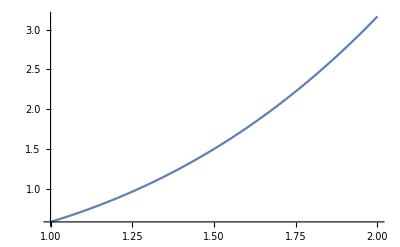

∫_1^2 √(1+(1/4+x^2)^2)ⅆx

2.78941

```mathematica
1.
f[x_] := ((x^3)/3) + (1/4x)
Plot[f[x], {x,1,2}]
Integrate[Sqrt[1+(f'[x])^2], {x,1,2}]
NIntegrate [Sqrt[1+(f'[x])^2], {x,1,2}]
```

```mathematica
The integrand does NOT have an antiderivative in terms of elementary functions
The arc length between 1 and 2 approximates to 2.78941
```

```mathematica
2.
```

clear[f]

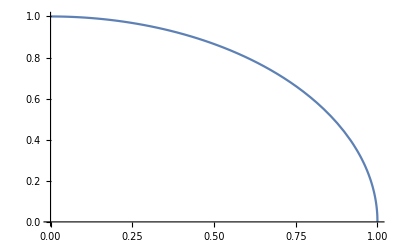

π/2

1.5708

```mathematica
clear[f]
f[x_] := Sqrt[1-x^2]
Plot[f[x], {x,0,1}]
Integrate[Sqrt[1+(f'[x])^2], {x,0,1}]
NIntegrate [Sqrt[1+(f'[x])^2], {x,0,1}]
```

```mathematica
The integrand does have an antiderivative in terms of elementary functions
The arc length between 0 and 1 approximates to 1.5708
```

```mathematica
3.
```

clear[f]

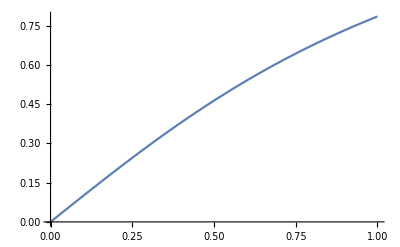

∫_0^1 √(1+1/((1+x^2)^2))ⅆx

1.27798

```mathematica
clear[f]
f[x_] := ArcTan[x]
Plot[f[x], {x,0,1}]
Integrate[Sqrt[1+(f'[x])^2], {x,0,1}]
NIntegrate [Sqrt[1+(f'[x])^2], {x,0,1}]
```

```mathematica
The integrand does NOT have an antiderivative in terms of elementary functions
The arc length between 0 and 1 approximates to 1.27798
```

```mathematica
4.
```

clear[f]

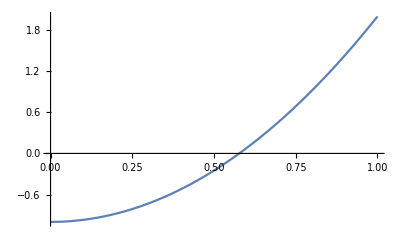

1/12 (6 √37+ArcSinh[6])

3.24903

```mathematica
clear[f]
f[x_] := 3x^2-1
Plot[f[x], {x,0,1}]
Integrate[Sqrt[1+(f'[x])^2], {x,0,1}]
NIntegrate [Sqrt[1+(f'[x])^2], {x,0,1}]
```

```mathematica
The integrand does have an antiderivative in terms of elementary functions
The arc length between 0 and 1 approximates to 3.24903
```

```mathematica
5.
```

clear[f]

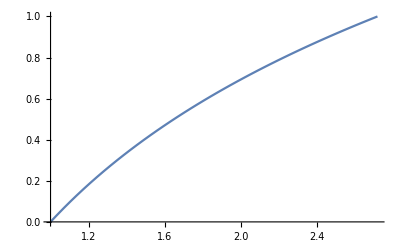

-√2+√(1+ⅇ^2)+ArcTanh[√2]-ArcTanh[√(1+ⅇ^2)]

2.0035

```mathematica
clear[f]
f[x_] :=Log[x]
Plot[f[x], {x,1,E}]
Integrate[Sqrt[1+(f'[x])^2], {x,1,E}]
NIntegrate [Sqrt[1+(f'[x])^2], {x,1,E}]
```

```mathematica
The integrand does have an antiderivative in terms of elementary functions
The arc length between 1 and E approximates to 2.0035
```

21.2

```mathematica
1.
```

```mathematica
rev[f_,a_,b_]:=Module[{t},
ParametricPlot3D[{x,f[x] Cos[t], f[x] Sin[t]},{x,a,b},{t,0,2Pi}]]
```

```mathematica
Clear[f,x]
f[x_]:= 8x/(1+x^2)
rev[f,0,10]
```

-Graphics3D-

```mathematica
Integrate[2Pi*f[x]*Sqrt[1+(f'[x])^2],{x,0,10}]
```

∫_0^10 (16 π x √(1+(-(16 x^2)/((1+x^2)^2)+8/(1+x^2))^2))/(1+x^2)ⅆx

```mathematica
NIntegrate[2Pi*f[x]*Sqrt[1+(f'[x])^2],{x,0,10}]
```

168.818

```mathematica
surface area = ∫_0^10 (16 π x √(1+(-(16 x^2)/((1+x^2)^2)+8/(1+x^2))^2))/(1+x^2)ⅆx
surface area ~= 168.818
```

```mathematica
2.
```

```mathematica
rev[f_,a_,b_]:=Module[{t},
ParametricPlot3D[{x,f[x] Cos[t], f[x] Sin[t]},{x,a,b},{t,0,2Pi}]]
```

```mathematica
Clear[f,x]
f[x_]:= Log[x]
rev[f,1,E]
```

-Graphics3D-